{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{5,-2.5,1.25,-0.625,0.3125,-0.15625,0.078125,-0.0390625,0.0195313,-0.00976563,0.00488281,-0.00244141,0.0012207,-0.000610352,0.000305176,-0.000152588,0.0000762939,-0.000038147,0.0000190735,-9.53674×10^-6,4.76837×10^-6,-2.38419×10^-6,1.19209×10^-6,-5.96046×10^-7,2.98023×10^-7,-1.49012×10^-7,7.45058×10^-8,-3.72529×10^-8,1.86265×10^-8,-9.31323×10^-9,4.65661×10^-9,-2.32831×10^-9,1.16415×10^-9,-5.82077×10^-10,2.91038×10^-10,-1.45519×10^-10,7.27596×10^-11,-3.63798×10^-11,1.81899×10^-11,-9.09495×10^-12,4.54747×10^-12,-2.27374×10^-12,1.13687×10^-12,-5.68434×10^-13,2.84217×10^-13,-1.42109×10^-13,7.10543×10^-14,-3.55271×10^-14,1.77636×10^-14,-8.88178×10^-15,4.44089×10^-15,-2.22045×10^-15,1.11022×10^-15,-5.55112×10^-16,2.77556×10^-16,-1.38778×10^-16,6.93889×10^-17,-3.46945×10^-17,1.73472×10^-17,-8.67362×10^-18,4.33681×10^-18,-2.1684×10^-18,1.0842×10^-18,-5.42101×10^-19,2.71051×10^-19,-1.35525×10^-19,6.77626×10^-20,-3.38813×10^-20,1.69407×10^-20,-8.47033×10^-21,4.23516×10^-21,-2.11758×10^-21,1.05879×10^-21,-5.29396×10^-22,2.64698×10^-22,-1.32349×10^-22,6.61744×10^-23,-3.30872×10^-23,1.65436×10^-23,-8.27181×10^-24,4.1359×10^-24,-2.06795×10^-24,1.03398×10^-24,-5.16988×10^-25,2.58494×10^-25,-1.29247×10^-25,6.46235×10^-26,-3.23117×10^-26,1.61559×10^-26,-8.07794×10^-27,4.03897×10^-27,-2.01948×10^-27,1.00974×10^-27,-5.04871×10^-28,2.52435×10^-28,-1.26218×10^-28,6.31089×10^-29,-3.15544×10^-29,1.57772×10^-29,0}

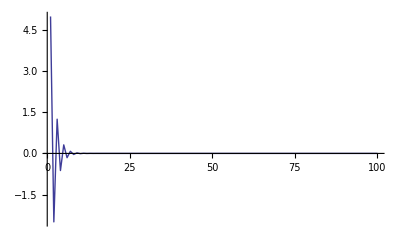

```mathematica
k=-0.5;
n=100;
p=ConstantArray[0,n]
p[[1]]=5;
For[i=2,i<n,i++,p[[i]]=k*p[[i-1]]]
p
ListLinePlot[p,PlotRange->All]
```

{5.,4.52419,4.09365,3.70409,3.3516,3.03265,2.74406,2.48293,2.24664,2.03285,1.8394,1.66436,1.50597,1.36266,1.23298,1.11565,1.00948,0.913418,0.826494,0.747843,0.676676,0.612282,0.554016,0.501294,0.45359,0.410425,0.371368,0.336028,0.30405,0.275116,0.248935,0.225246,0.203811,0.184416,0.166866,0.150987,0.136619,0.123618,0.111854,0.10121,0.0915782,0.0828634,0.0749779,0.0678428,0.0613867,0.055545,0.0502592,0.0454764,0.0411487,0.0372329,0.0336897,0.0304837,0.0275828,0.024958,0.0225829,0.0204339,0.0184893,0.0167298,0.0151378,0.0136972,0.0123938,0.0112143,0.0101472,0.00918152,0.00830779,0.0075172,0.00680184,0.00615456,0.00556888,0.00503893,0.00455941,0.00412552,0.00373293,0.00337769,0.00305626,0.00276542,0.00250226,0.00226414,0.00204867,0.00185372,0.00167731,0.0015177,0.00137327,0.00124258,0.00112434,0.00101734,0.000920529,0.000832929,0.000753665,0.000681945,0.000617049,0.000558329,0.000505197,0.000457121,0.00041362,0.000374259,0.000338644,0.000306417,0.000277258,0.000250873,0.000227}

{-0.475813,-0.430533,-0.389563,-0.352491,-0.318947,-0.288595,-0.261132,-0.236282,-0.213797,-0.193451,-0.175042,-0.158384,-0.143312,-0.129674,-0.117334,-0.106168,-0.096065,-0.0869232,-0.0786513,-0.0711667,-0.0643943,-0.0582663,-0.0527216,-0.0477045,-0.0431648,-0.0390571,-0.0353403,-0.0319773,-0.0289342,-0.0261808,-0.0236893,-0.021435,-0.0193952,-0.0175495,-0.0158794,-0.0143683,-0.013001,-0.0117638,-0.0106443,-0.00963136,-0.00871482,-0.00788549,-0.00713509,-0.0064561,-0.00584172,-0.0052858,-0.00478279,-0.00432765,-0.00391582,-0.00354318,-0.003206,-0.00290091,-0.00262485,-0.00237506,-0.00214905,-0.00194454,-0.00175949,-0.00159205,-0.00144055,-0.00130346,-0.00117942,-0.00106719,-0.000965629,-0.000873738,-0.00079059,-0.000715356,-0.000647281,-0.000585684,-0.000529949,-0.000479517,-0.000433885,-0.000392596,-0.000355235,-0.00032143,-0.000290842,-0.000263165,-0.000238121,-0.000215461,-0.000194957,-0.000176405,-0.000159617,-0.000144428,-0.000130684,-0.000118248,-0.000106995,-0.0000968129,-0.0000875999,-0.0000792637,-0.0000717207,-0.0000648956,-0.00005872,-0.000053132,-0.0000480759,-0.0000435008,-0.0000393612,-0.0000356155,-0.0000322262,-0.0000291595,-0.0000263846,-0.0000238738}

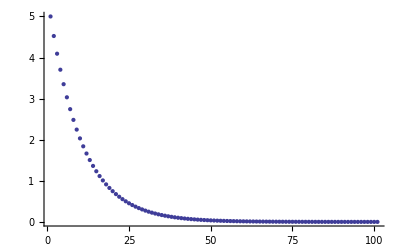

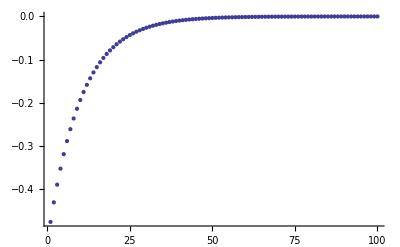

Plot::pllim: Range specification {t, 0, 10, 0.1} is not of the form {x, xmin, xmax}.

Plot[-s Exp[-s t],{t,0,10,0.1}]

```mathematica
decay=Table[5*Exp[-1*t],{t,0,10,0.1}]
decayDt=Differences[decay]
ListPlot[decay]
ListPlot[decayDt]
Plot[-s Exp[-s*t],{t,0,10,0.1}]
```

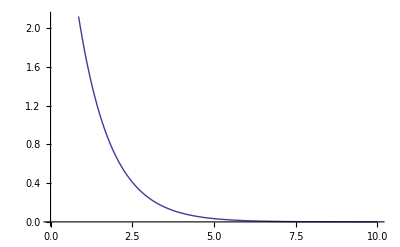

{{y[x]→ⅇ^(2 x)}}

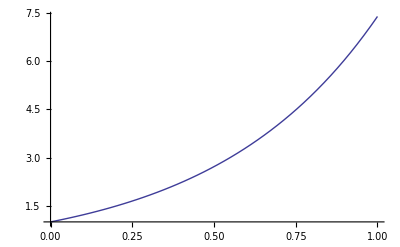

{{m[t]→c}}

{{m→InterpolatingFunction[{{0.,10.}},<>]}}

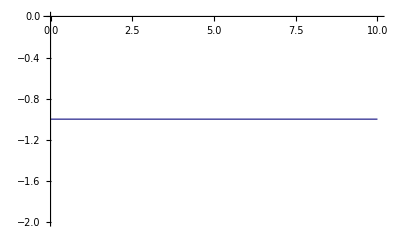

```mathematica
Clear["Global`*"]
DSolve[{y'[x]==2y[x],y[0]==1},y[x],x]
Plot[y[x]/.%,{x,0,1}]

DSolve[{m'[t]==-D[k m[t],t],m[0]==c},m[t],t]

s=NDSolve[{m'[t]==-D[k m[t],t],m[0]==-1},m,{t,0,10}]
Plot[Evaluate[m[t]/.s],{t,0,10},PlotRange->All]
```